```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Get["../lib/lib2.m"];
Get["../lib/util.m"];
```

```mathematica
plotsDir= "../../plots/plots-104/";
If[!DirectoryQ[plotsDir], CreateDirectory[plotsDir]];
```

```mathematica
liststd ={};
Restd ={};
Imstd ={};
ReImstd = {};
```

```mathematica
Table[Module[{fn,data,matdata,mns,vars,Kval},Kval=5;
(*fn=FileNames[All,"./runs/Trials/N"<>ToString[Nval]<>"K"<>ToString[Kval]];
Print["Computing for N="<>ToString[Nval]];
data=Import[#]&/@fn;*)
Print["Changing N and K"];
data = {Import["../../runs/Trials/N3K5/37797394.dat"],Import["../../runs/Trials/N3K5/56394678.dat"]};
changeNK[Nval,Kval];
Print["cMat"];
matdata=(cMatOne/@#)&/@data;
Print["Computing Std"];
stdN =Around[Table[(1/StandardDeviation[($N)/(√($N-1))Map[Diagonal,matdata[[d]][[All,2;;$K+1]],{2}]//Flatten])^2,{d,1,Length[matdata]}]];
reimlist =Table[Join[
Flatten@Table[($N)/(√($N-1)) matdata[[d]][[All, 2;;, a, a]], {a, 1, $N}],
Flatten@Table[√(2$N)ReIm@matdata[[d]][[All, 2;;, a, b]], {a, 1, $N}, {b, a+1, $N}]
]//Chop,{d,1,Length[matdata]}];
(*reimlist =Table[Table[Table[Table[matdata[[d]][[m,k+1]][[i,j]],{i,1,3},{j,1,i-1}]//Flatten,{k,1,$K}]//Flatten,{m,1,Length[matdata[[1]]]}]//Flatten,{d,1,Length[matdata]}];*)
ristd  =Around[(1/(StandardDeviation/@reimlist))^2];
(*re =Around@ (1/(StandardDeviation/@Re[reimlist]))^2;
im= Around@(1/(StandardDeviation/@Im[reimlist]))^2;
AppendTo[Restd,{Nval,re}];
AppendTo[Imstd,{Nval,im}];*)
AppendTo[ReImstd,{Nval,ristd}];
(*Export["listStd.mx",liststd];
Export["reImStd.mx",ristd];*)
(*Export["reStd.mx",Restd];
Export["ImStd.mx",Imstd];*)

Print["Computing COMPLETE for N="<>ToString[Nval]];],{Nval,3,3}];
```

Changing N and K

cMat

Computing Std

Computing COMPLETE for N=3

```mathematica
ReImstd
```

{{3,7.530.17}}

```mathematica
reimlist//Length
```

2

```mathematica
(1/(StandardDeviation/@reimlist))^2
```

{7.64602,7.64602}

```mathematica
1/({2}^2)
```

{1/4}

```mathematica
Join[
Flatten@Table[($N)/(√($N-1)) cmatdata[[All, 2;;, a, a]], {a, 1, $N}],
Flatten@Table[√(2$N)ReIm@cmatdata[[All, 2;;, a, b]], {a, 1, $N}, {b, a+1, $N}]
]//Chop
```

```mathematica
data = Import["../../runs/Trials/N3K5/37797394.dat"];
```

```mathematica
data[[1]]
```

{0,-0.246574,-0.353697,-0.566037,-0.552423,-0.248268,-0.196131,-0.0156671,-0.22891,-0.266684,0.655524,-0.323508,0.205716,-0.213912,0.431211,0.298225,-0.209468,-0.057558,0.168638,-0.0738947,0.288131,-0.131629,0.534358,-0.45033,0.0682711,-0.541116,-0.24798,0.39376,-0.294439,-0.571241,-0.232338,0.0372728,0.523484,-0.535461,-0.319261,-0.693604,0.51527,-0.517782,0.657802,-0.0660656,-0.135282,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
(*Export["listStd.mx",liststd];*)
```

```mathematica
(*Export[plotsDir<>"/Plot_of_Std_alpha.pdf",pltmns,ImageResolution->300,ImageSize->500];
*)
```

```mathematica
liststd = Import["..//..//scripts//listStd.mx"];
ReImdata = Import["..//..//scripts//reImStd.mx"];
```

```mathematica
ReImdata[[1,2]]
```

$Aborted

```mathematica
ListLinePlot[ReImdata]
```

$Aborted

```mathematica
liststd
```

{{3,15.00.4},{4,18.80.4},{5,22.00.5},{6,24.60.5},{7,27.10.4},{8,29.330.33},{9,31.350.22}}

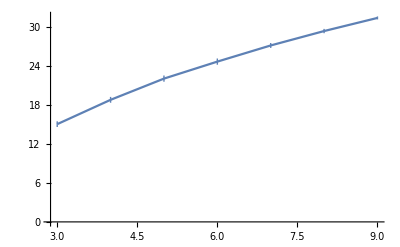

```mathematica
ListLinePlot[{liststd}]
```

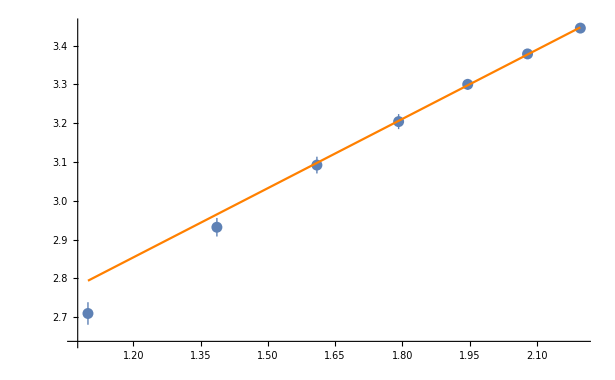

```mathematica
Show[
ListPlot[Log@liststd,PlotRange->All],
Plot[lm[x], {x, Log[3], Log[9]}, PlotStyle->Orange]
]
```

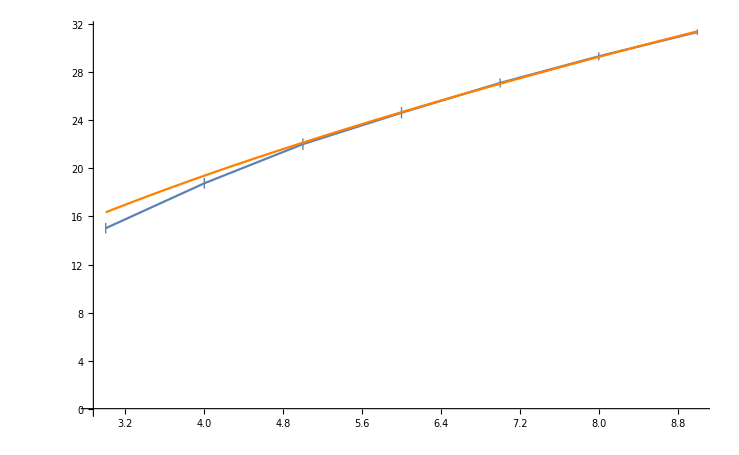

```mathematica
Show[
ListLinePlot[{liststd},PlotRange->All],
Plot[Exp[lm[Log[$N]]], {$N, 3, 9},
PlotStyle->Orange
]
]
```

```mathematica
d = {Log[#[[1]]], Log[#[[2]]["Value"]]}&/@liststd//Take[#, -4]&
```

{{Log[6],3.20413},{Log[7],3.30018},{Log[8],3.37863},{Log[9],3.4452}}

```mathematica
lm = LinearModelFit[d, {x}, x]
```

FittedModel[2.1406+0.594654 x]